```mathematica
f[x_]=x^2-Cos[x]
```

x^2-Cos[x]

```mathematica
x^2-Cos[x]
```

x^2-Cos[x]

```mathematica
NewtonRaphsonstep[x_]=x-f[x]/f'[x];
```

```mathematica
NewtonRaphsonstep[0.5]
```

0.924207

```mathematica
0.9242069272931975
```

```mathematica
0.9242069272931975
```

0.924207

Para guardar todas las soluciones de las n iteraciones:

```mathematica
NewtonRaphson[x0_,n_]:=Block[{soluciones = {x0},x = x0},
Do[
x = NewtonRaphsonstep[x];
AppendTo[soluciones,x]; (* Añado el nuevo x a la lista *)
,
n (* Número de repeticiones *)
];

soluciones
];
```

```mathematica
listaDeSoluciones=NewtonRaphson[0.2, 10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

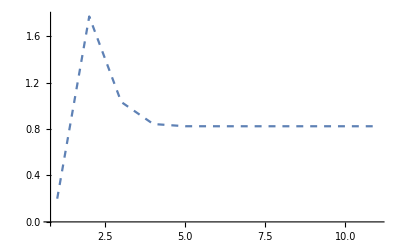

```mathematica
ListLinePlot[listaDeSoluciones,PlotRange->All, PlotStyle->Dashed]
```

```mathematica
Error[x_]=Abs[-f''[x]/2f'[x]]
```

1/2 Abs[(-2-Cos[x]) (2 x+Sin[x])]

```mathematica
ListadeErrores=Map[Error,{listaDeSoluciones}]
```

{{0.892037,4.07282,3.67436,3.24265,3.19177,3.19122,3.19122,3.19122,3.19122,3.19122,3.19122}}

{{-0.892037,-4.07282,-3.67436,-3.24265,-3.19177,-3.19122,-3.19122,-3.19122,-3.19122,-3.19122,-3.19122}}

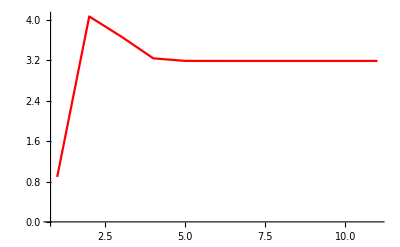

```mathematica
{{-0.8920372319404721,-4.072819573463018,-3.674360504309449,-3.242652921241367,-3.191768318896348,-3.1912194031656482,-3.191219340739203,-3.191219340739202,-3.191219340739202,-3.191219340739202,-3.191219340739202}}
ListLinePlot[ListadeErrores, PlotRange->All, PlotStyle->Red]
```